```mathematica
(* Let's try a dark energy potential that Amy will be studying *)

(* first let's use the diff eq method *)

h=1/√2;V[x_]:=7/(48(.005)) (ⅇ^(-2x/7.637626158259733)-2 ⅇ^(-x/7.637626158259733)+1.1905508 ⅇ^(-2/3 x/7.637626158259733))
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.200339}

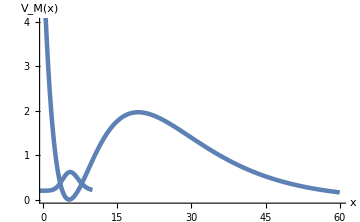

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],Plot[V[x],{x,.5,60},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],PlotRange->{{.5,60},{0,4}},AxesOrigin->{-5,0},ImageSize->Medium]
```

```mathematica
(* Now let's try the Matrix method with the osc basis 16x16 *)

s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{16,16}]
```

SparseArray[…]

```mathematica
Xosc:=N[s+Transpose[s]]
```

```mathematica
Posc:= ⅈ/2 N[(-s+Transpose[s])]
```

```mathematica
Hdarkenergyosc:= .5Posc.Posc+7/(48(.005))(MatrixExp[-2Xosc/7.637626158259733]- 2 MatrixExp[-Xosc/7.637626158259733] + 1.1905508 MatrixExp[-2/3 Xosc/7.637626158259733])
```

```mathematica
Reverse[N[Eigenvalues[Hdarkenergyosc]]]
```

{0.213492,0.6952,1.31164,2.07659,2.99911,4.11168,5.48704,7.25115,9.58505,12.7282,17.0017,22.8644,31.022,42.6641,60.0965,89.2154}

```mathematica
Hdarkenergyosc=Chop[Hdarkenergyosc];
SetDirectory[NotebookDirectory[]];
saveHam[ham_] :=Export["./"<>"Hdarkenergyosc16x16.txt", ham, "Table"]

saveHam[Hdarkenergyosc];
```

```mathematica
(* Lets try it again with 32x32 *)

s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{32,32}]
```

SparseArray[…]

```mathematica
Xosc:=N[s+Transpose[s]]
```

```mathematica
Posc:= ⅈ/2 N[(-s+Transpose[s])]
```

```mathematica
Hdarkenergyosc:= .5Posc.Posc+7/(48(.005))(MatrixExp[-2Xosc/7.637626158259733]- 2 MatrixExp[-Xosc/7.637626158259733] + 1.1905508 MatrixExp[-2/3 Xosc/7.637626158259733])
```

```mathematica
Reverse[N[Eigenvalues[Hdarkenergyosc]]]
```

{0.200346,0.580535,0.939147,1.31098,1.74025,2.24007,2.80804,3.4415,4.13969,4.90362,5.73608,6.6419,7.62871,8.70841,9.90155,11.249,12.8274,14.7487,17.143,20.1473,23.9118,28.6144,34.4785,41.7938,50.9444,62.4523,77.0483,95.7979,120.343,153.437,200.379,274.654}

```mathematica
Hdarkenergyosc=Chop[Hdarkenergyosc];
SetDirectory[NotebookDirectory[]];
saveHam[ham_] :=Export["./"<>"Hdarkenergyosc32x32.txt", ham, "Table"]

saveHam[Hdarkenergyosc];
```